```mathematica
θ=0.58;
V[x1_,x2_,d_,θ_]:=1/d-1/(√(d^2+2d Cos[θ]x1+x1^2))-1/(√(d^2-2d Cos[θ]x2+x2^2))+1/(√(d^2-2d Cos[θ](x2-x1)+(x2-x1)^2))+1/2 x1^2+1/2 x2^2
$Post=Chop[#,10^-7]&;
energ=Module[{d,eqs,s,min,minPot,energies},
energies={};
Do[
d=i/10;
eqs={Together[D[V[x1,x2,d,θ],{x1,1}]]//Together//Numerator,Together[D[V[x1,x2,d,θ],{x2,1}]]//Together//Numerator}//FullSimplify;
s=NSolve[eqs,{x1,x2},Reals];
min=Sort[s,(V[x1,x2,d,θ]/.#1)<=(V[x1,x2,d,θ]/.#2) &][[1]];
minPot=V[x1,x2,d,θ]/.min;
AppendTo[energies,{d,minPot}];
,{i,0.1*10,3.5*10}];
energies
];
```

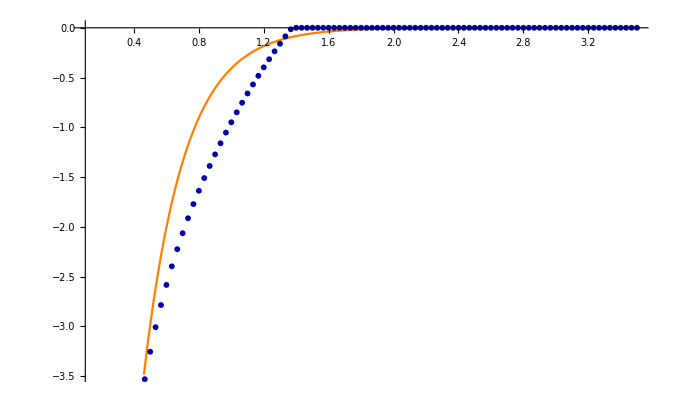

```mathematica
f[x_]:=Normal[NonlinearModelFit[energ[[;;]],-De Exp[-a r],{De,a},r,MaxIterations->∞]]/.r->x
Show[Plot[f[x],{x,0.1,3.5},PlotStyle->{Orange}],ListPlot[energ,PlotMarkers->{Automatic,6},PlotStyle->Darker[Blue]]]
```

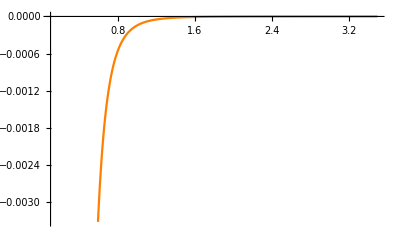

```mathematica
f[x_]:=Normal[NonlinearModelFit[energ,a/r^6+b/r^12,{a,b},r,MaxIterations->∞]]/.r->x
Show[Plot[f[x],{x,0.1,3.5},PlotStyle->{Orange}],ListPlot[energ,PlotMarkers->{Automatic,6},PlotStyle->Darker[Blue]]]
```

```mathematica
{Together[D[V[x1,x2,d,θ],{x1,1}]]//Together//Numerator,Together[D[V[x1,x2,d,θ],{x2,1}]]//Together//Numerator}//FullSimplify
```

{-0.836463 (1. d (d^2+1.67293 d x1+x1^2)^(3/2)+1.19551 x1 (d^2+1.67293 d x1+x1^2)^(3/2)-1. d (d^2+(x1-x2)^2+1.67293 d (x1-1. x2))^(3/2)-1.19551 x1 (d^2+(x1-x2)^2+1.67293 d (x1-1. x2))^(3/2)-1.19551 x1 (d^2+1.67293 d x1+x1^2)^(3/2) (d^2+(x1-x2)^2+1.67293 d (x1-1. x2))^(3/2)-1.19551 (d^2+1.67293 d x1+x1^2)^(3/2) x2),0.836463 (-1. d (d^2+(x1-x2)^2+1.67293 d (x1-1. x2))^(3/2)+1.19551 (d^2+(x1-x2)^2+1.67293 d (x1-1. x2))^(3/2) x2+1. d (d^2-1.67293 d x2+x2^2)^(3/2)+1.19551 x1 (d^2-1.67293 d x2+x2^2)^(3/2)-1.19551 x2 (d^2-1.67293 d x2+x2^2)^(3/2)+1.19551 (d^2+(x1-x2)^2+1.67293 d (x1-1. x2))^(3/2) x2 (d^2-1.67293 d x2+x2^2)^(3/2))}

```mathematica
D[V[x1,x2,d,θ],{x1,1}]//Together//Numerator
```

-0.836463 d (d^2+1.67293 d x1+x1^2)^(3/2)-1. x1 (d^2+1.67293 d x1+x1^2)^(3/2)+(d^2+1.67293 d x1+x1^2)^(3/2) x2+0.836463 d (d^2-1.67293 d (-x1+x2)+(-x1+x2)^2)^(3/2)+x1 (d^2-1.67293 d (-x1+x2)+(-x1+x2)^2)^(3/2)+x1 (d^2+1.67293 d x1+x1^2)^(3/2) (d^2-1.67293 d (-x1+x2)+(-x1+x2)^2)^(3/2)